```mathematica
z0=800*10^(-3); (*mm*)
lam = 5320*10^(-10); (*А*)
Object=50.0*10^(-3);
Xbeg=-Object/2.0;
Xend=Object/2.0;
JK = Import["x_dPhi.txt", "Table"];
JKleft=Table[{-Object/2+(JK[[2,1]]-JK[[1,1]])*i, -Object/2+(JK[[2,1]]-JK[[1,1]])*i, JK[[1,3]]},{i,0,(JK[[1,1]]-(-Object/2))/(JK[[2,1]]-JK[[1,1]])-1,1}];
JKright=Table[{-JK[[1,1]]+(JK[[2,1]]-JK[[1,1]])*i, -JK[[1,1]]+(JK[[2,1]]-JK[[1,1]])*i, JK[[Length[JK],3]]},{i,0,(JK[[1,1]]-(-Object/2))/(JK[[2,1]]-JK[[1,1]]),1}];
HalfLeft=Table[{-Object/2+(JK[[2,1]]-JK[[1,1]])*i, -Object/2+(JK[[2,1]]-JK[[1,1]])*i, JK[[1,3]]},{i,0,(0-Xbeg)/(JK[[2,1]]-JK[[1,1]])-1,1}];

HalfRight=Table[{0+(JK[[2,1]]-JK[[1,1]])*i, -JK[[1,1]]+(JK[[2,1]]-JK[[1,1]])*i, JK[[Length[JK],3]]},{i,0,(JK[[1,1]]-(-Object/2))/(JK[[2,1]]-JK[[1,1]]),1}];WindowNS=Join[JKleft,JK,JKright];
WindowJump=Join[HalfLeft,HalfRight];
WindowHole=Join[JKleft,JKright];
```

/home/mikhail/Diffraction

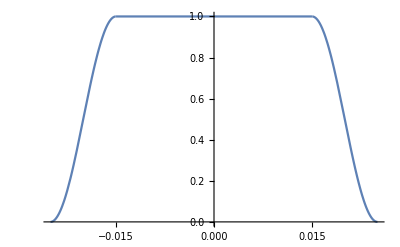

```mathematica
A[xw_]:=If[(xw-Xbeg)≤10.0*10^(-3),Sin[Pi/2/(10*10^(-3))*(xw-Xbeg)]^2,If[(xw-Xbeg)≥(Object-10.0*10^(-3)),Sin[Pi/2/(10*10^(-3))*((xw-Xbeg)-Object)]^2,1.0]];
Plot[A[x],{x,Xbeg,Xend},PlotRange->Full]
```

```mathematica
x[j_]:=WindowNS[[j,2]];
dPhi[j_]:=WindowNS[[j,3]];
r[j_,xp_]:=Sqrt[z0*z0+(x[j]-xp)*(x[j]-xp)];
steps = Length[WindowNS];
ResultNS[xp_]:=Sum[A[x[j]]*(z0/r[j,xp])^0.5*Exp[2*I*Pi / lam * (r[j,xp]-z0)+I*dPhi[j]], {j,1, steps}];
NExperimentNS=Table[{xp,Re[ResultNS[xp]*Conjugate[ResultNS[xp]]]},{xp,-6.0*10^(-3),6.0*10^(-3),0.02*10^(-3)}];
toStr[{x_,y_}]:=ToString[x]<>" "<>ToString[y]<>"\n"
WriteString[OpenWrite["ExperimentNSx0p5.out"],StringJoin[toStr/@NExperimentNS]];
Close["ExperimentNSx0p5.out"]
```

C:\Users\Maxim Timokhin\Google Диск\science\main results\problems\shock_tube\dif\diff_mathematica\trajectory_diffraction\ExperimentNSx0p5.out

```mathematica
x[j_]:=WindowJump[[j,2]];
dPhi[j_]:=WindowJump[[j,3]];
r[j_,xp_]:=Sqrt[z0*z0+(x[j]-xp)*(x[j]-xp)];
steps = Length[WindowJump];
ResultJump[xp_]:=Sum[A[x[j]]*(z0/r[j,xp])^0.5*Exp[2*I*Pi / lam * (r[j,xp]-z0)+I*dPhi[j]], {j,1, steps}];
NExperimentJump=Table[{xp,Re[ResultJump[xp]*Conjugate[ResultJump[xp]]]},{xp,-6.0*10^(-3),6.0*10^(-3),0.02*10^(-3)}];
toStr[{x_,y_}]:=ToString[x]<>" "<>ToString[y]<>"\n"
WriteString[OpenWrite["ExperimentJump.out"],StringJoin[toStr/@NExperimentJump]];
Close["ExperimentJump.out"]
```

C:\Users\Maxim Timokhin\Google Диск\science\main results\problems\shock_tube\dif\diff_mathematica\trajectory_diffraction\ExperimentJump.out

```mathematica
x[j_]:=WindowHole[[j,2]];
dPhi[j_]:=WindowHole[[j,3]];
r[j_,xp_]:=Sqrt[z0*z0+(x[j]-xp)*(x[j]-xp)];
steps = Length[WindowHole];
ResultNS[xp_]:=Sum[A[x[j]]*(z0/r[j,xp])^0.5*Exp[2*I*Pi / lam * (r[j,xp]-z0)+I*dPhi[j]], {j,1, steps}];
NExperimentNS=Table[{xp,Re[ResultNS[xp]*Conjugate[ResultNS[xp]]]},{xp,-6.0*10^(-3),6.0*10^(-3),0.02*10^(-3)}];
toStr[{x_,y_}]:=ToString[x]<>" "<>ToString[y]<>"\n"
WriteString[OpenWrite["ExperimentHole.out"],StringJoin[toStr/@NExperimentNS]];
Close["ExperimentHole.out"]
```

C:\Users\Maxim Timokhin\Google Диск\science\main results\problems\shock_tube\dif\diff_mathematica\trajectory_diffraction\ExperimentHole.out